# Ticks with CustomTicks & MathPSfrag

## Preamble

```mathematica
SetDirectory@NotebookDirectory[];
Needs@"CustomTicks`";
Needs@"MathPSfrag`";
Needs@"EqualTicks`";
EmptyTicks[a_,b_] := LinTicks[a, b, ShowTickLabels->False]
```

```mathematica
SetOptions[LinTicks,
MajorTickLength->{0.02,0},
  MinorTickLength->{0.01,0}];
```

```mathematica
f[x_]:=10x+ 20Sin[x]
g1=Plot[f[x],{x,-10,10},
FrameTicks->{LinTicks,LinTicks,EmptyTicks,EmptyTicks},
Frame->True];
```

## Default exporting with CustomTicks

The ticks sizes in x and y are the same. 
(Note the padding in the tick ranges needs adjusting, though.)

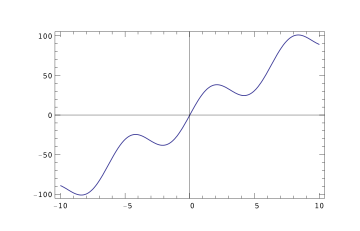

```mathematica
Export["test.pdf",g1];
Show@Import@"test.pdf"
```

## Exporting with MathPSfrag & CustomTicks

Now the ticks are scaled by the aspect ratio.
Also note that the combination of CustomTicks and MathPSfrag has somehow changed the numbers to be typeset in text, rather than maths, mode.

```mathematica
PSfragExport["test1",g1]//UnPSfrag
```

Low resolution preview of UnPSfrag'ed image:

-Graphics-

## Forcing equal tick sizes with MathPSfrag & CustomTicks

With EqualTicks, things are nice again. 
Note that the PlotRangePadding now scales with the tick size.

```mathematica
EqualTicks[Plot];
g3=Plot[f[x],{x,-10,10},Frame->True];
PSfragExport["test2",g3]//UnPSfrag
```

Low resolution preview of UnPSfrag'ed image:

-Graphics-

## Changing the parameters

```mathematica
EqualTicks[Plot,
AspectRatio -> 1,
FrameTicks->{EmptyXTicks,EmptyYTicks,XTicks,YTicks},
TickLength -> {0.05,0},
MinorTickLength -> {0.025,0},
PadRatio -> 1
];
```

```mathematica
g4=Plot[f[x],{x,-10,10},Frame->True];
PSfragExport["test2",g4]//UnPSfrag
```

Low resolution preview of UnPSfrag'ed image:

-Graphics-